# -Graphics-

# Wolfram 语言编程：概念到应用

## 神经网络、网页操作和图像处理

-Graphics-

## 学习目标

### 神经网络

构建网络的基本组件

层、链和图

训练

网络“手术”

应用领域

### 网页操作

将表达式部署到网页

从互联网导入数据

连接到外部服务

### 图像处理

基本图像操作

分量/组件识别

像素级操作

卷积

使用神经网络

# 神经网络

## 基本原理

神经网络是一种计算结构，旨在模仿生物“学习”的方式.

在生物学中，当给一个神经元足够强的刺激时，它会激发并将化学信息发送给其他神经元. 这可以刺激其他神经元等等.

在神经网络中对此进行模拟，我们使用“权重”确定一个神经元对另一神经元的影响程度，以及每个神经元有一个激活函数.

#### 结构体

在构建神经网络时，我们不必担心每个神经元. 我们将它们分为多个层，然后相互连接.

我们将从系列中只有几层的非常简单的网络开始，但是我们可以将其扩展为更复杂的结构.  Wolfram 语言™的语法使构建网络变得简单.

#### 用法

当人类正在学习时，必须“告诉”给定的结果是否“正确”. 我们学会将狗与猫区分开来，因为我们看到了许多以一种或另一种方式“贴上标签”的例子.

我们必须使用精选的数据集训练神经网络，改变神经元之间的权重，以使网络的准确性最大化. 这是在高维空间上的优化问题！

#### 要点

神经网络擅长将大量原始数据转换为较小数量的相关或有趣数据的任务.

将音频文件映射到单词（语音识别）

将图像映射到图像内容或特征（计算机视觉）

将文本解析为语义解释

我们将学习如何组合神经网络，然后对其进行训练，使它们执行某些任务.

#### 先决条件

1. 指定您的网络体系结构. 关于多少层，什么类型的层等存在大量的“民俗学”. 如果一些方法均失败，可以试试其他的.

2. 要训练网络，我们需要知道给定输入所需的输出. 我们需要许多示例来训练我们的网络.

3.（可选）选择训练详细信息，例如损失函数、学习参数等. 默认情况下，NetTrain 函数会自动选择这些细节.

## 网络结构

### 层和连接

在构建神经网络时，我们从以指定方式相互通信的层构建神经网络.  一些简单且常用的图层类型是：

LinearLayer — 计算基本的 M·x⃗+b⃗ 矩阵-向量乘积

```mathematica
linear=NetInitialize@LinearLayer[3,"Input"->3]
```

LinearLayer[<>]

```mathematica
linear[{0,1,3}]
```

{1.12456,-0.644516,0.998569}

ElementwiseLayer — 对每个输入独立执行指定的数学运算

```mathematica
elem=ElementwiseLayer[#^2&]
```

ElementwiseLayer[<>]

```mathematica
elem[{1,3,5}]
```

{1.,9.,25.}

ConvolutionLayer — 计算具有给定内核大小的卷积，表示”相邻”神经元的总和

DropoutLayer — 指示训练过程随机丢弃给定的神经元，以确保结果可靠

paclet:ref/SoftmaxLayerSoftmaxLayer— 归一化输出矢量，使其适于解释为概率

```mathematica
softmax=SoftmaxLayer["Input"->3]
```

SoftmaxLayer[<>]

```mathematica
softmax[{1,2,3}]
```

{0.0900306,0.244728,0.665241}

```mathematica
Total[%]
```

1.

您可以在 主要的神经网络指南.中找到所有图层的完整列表.

#### NetChain

NetChain 允许我们将多个网络层串联在一起.

如果没有明确给出网络层的维度，NetChain 将自动确定它们.

某些类型的图层允许设置其输出的维度，例如 LinearLayer [4] 返回一个四分量向量. 它们的输入维度会自动设置为与上一层的输出一致：

```mathematica
myNetChain= NetChain[{LinearLayer[4],DropoutLayer[],ElementwiseLayer[Round],LinearLayer[2],SoftmaxLayer[]},"Input"->2]
```

NetChain[<>]

#### NetGraph

NetGraph 允许我们以更复杂的方式将链和层连接在一起，并指定多个输入和输出.

我们在给定的元素列表中使用规则及其指标指定它们的连接方式：

```mathematica
NetGraph[{myNetChain,myNetChain,myNetChain},{1->2,1->3}]
```

NetGraph[<>]

另外，我们可以为图中的节点分配名称，并使用名称代替指标：

```mathematica
myNetGraph=NetGraph[<|"mylayer1"->myNetChain,"mylayer2"->myNetChain,"mylayer3"->myNetChain|>,{"mylayer1"->"mylayer2","mylayer1"->"mylayer3"}]
```

NetGraph[<>]

当我们指定 NetGraph 时，权重尚未初始化. 在训练之前，我们需要使用 NetInitialize.

#### NetInitialize

```mathematica
myInitializedNetGraph=NetInitialize[myNetGraph]
```

NetGraph[<>]

#### 获取有关网络的信息

标准 Wolfram 语言函数 Information 可以为您提供有关网络的基本详细信息：

```mathematica
Information[myInitializedNetGraph]
```

Net Information

为 Information 指定第二个参数可以为我们提供更多特定的属性：

```mathematica
Information[myInitializedNetGraph,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[myInitializedNetGraph,"LayerTypeCounts"]
```

<|LinearLayer→6,DropoutLayer→3,ElementwiseLayer→3,SoftmaxLayer→3|>

#### 使用网络

一旦指定了图的结构并初始化了权重，它便成为一个可以接受指定形式的输入并返回指定形式的输出的函数：

```mathematica
myInitializedNetGraph[{.3,.1}]
```

<|Output1→{0.442819,0.557181},Output2→{0.0893846,0.910615}|>

此输出具有正确的形式，但本质上是随机的. 该网络还没有做任何有用的事情，因为我们还没有训练它做任何事情！

## 训练网络

#### 线性回归

在最低限度上，训练神经网络只是执行最小二乘线性回归. 我们有一组输入及其相应的输出，通过调整网络的自由参数，以使误差（“损失”）最小化：

```mathematica
trainedLinearFunction=NetTrain[LinearLayer[],{1->1.9,2->4.1,3->6.0,4->8.1}]
```

LinearLayer[<>]

因为我们的函数接受一个实数输入并返回一个实数输出，所以我们可以将其用作实数变量的普通函数：

```mathematica
trainedLinearFunction[2.5]
```

5.16397

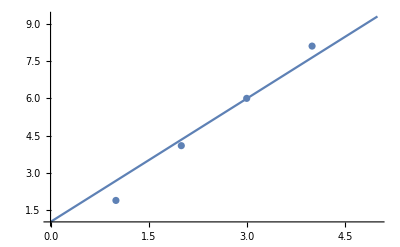

```mathematica
Show[Plot[trainedLinearFunction[x],{x,0,5}],ListPlot[{{1,1.9},{2,4.1},{3,6.0},{4,8.1}}]]
```

尽管可能需要更复杂的网络，但这也适用于更复杂的函数.

#### 更一般的函数回归

我们选择一个更复杂的函数，例如 Exp[-Norm[{x,y}]].  要训练我们的网络，我们需要大量的数据点，为网络输入对和相应的期望输出提供训练数据：

```mathematica
Plot3D[Exp[-Norm[{x,y}]],{x,-4,4},{y,-4,4},NormalsFunction->None,PlotRange->All,MaxRecursion->5]
```

-Graphics3D-

```mathematica
expFunctionData=Flatten@Table[{x,y}->Exp[-Norm[{x,y}]],{x,-3,3,.005},{y,-3,3,.005}];
```

```mathematica
expFunctionData[[1;;5]]
```

{{-3.,-3.}→0.0143696,{-3.,-2.995}→0.0144205,{-3.,-2.99}→0.0144715,{-3.,-2.985}→0.0145226,{-3.,-2.98}→0.0145739}

NetChain 允许为其参数使用一些简短的符号：

Tanh 之类的函数等效于 ElementwiseLayer [Tanh]

诸如 32 的整数等效于 LinearLayer [32]

```mathematica
netForFittingExp=NetChain[{32,Tanh,1}];
```

```mathematica
trainedExpFunction=NetTrain[netForFittingExp,expFunctionData,BatchSize->1024]
```

NetChain[<>]

```mathematica
GraphicsRow[{Plot3D[trainedExpFunction[{x,y}],{x,-4,4},{y,-4,4},NormalsFunction->None,PlotRange->All],Plot3D[Exp[-Norm[{x,y}]],{x,-4,4},{y,-4,4},NormalsFunction->None,PlotRange->All,MaxRecursion->5]}]
```

-Graphics-

#### 分类数据

我们还可以使用网络将数据分类.

让我们获取 2D 点. 如果 x 坐标为正，我们希望结果为 1，否则为 2：

```mathematica
classifiableData=Module[{q},Table[{(q=RandomReal[{-4,4},2]),If[q[[1]]>0,1,2]},{i,1,100}]]
```

{{{3.58492,-3.29619},1},{{-1.63599,-0.247961},2},{{1.11903,2.11127},1},{{2.6478,3.93199},1},{{3.98553,-1.37459},1},{{-0.218133,2.25497},2},{{3.95107,3.87371},1},{{-0.441599,0.375168},2},{{-2.66666,3.24866},2},{{3.43133,-0.650164},1},{{2.95237,1.36609},1},{{-1.23459,-3.15908},2},{{-3.40231,-2.11308},2},{{2.04384,1.34031},1},{{-2.90687,-2.18196},2},{{2.63764,0.348842},1},{{2.57358,0.407288},1},{{1.56133,-1.52313},1},{{-0.381822,-1.71243},2},{{2.02465,-3.00323},1},{{-3.77228,0.249488},2},{{-0.216157,-1.84955},2},{{-0.643031,2.24865},2},{{-1.67399,2.97757},2},{{-1.16911,-1.98874},2},{{-0.139533,-2.38123},2},{{-0.825638,-1.23088},2},{{1.36167,-1.99154},1},{{-0.69202,-0.325986},2},{{3.56342,-3.70525},1},{{-1.06535,2.68825},2},{{0.798381,3.52534},1},{{-2.8814,-1.51061},2},{{1.89209,2.01352},1},{{-2.61244,-1.65281},2},{{3.45424,0.291634},1},{{1.67706,-3.0451},1},{{-1.66587,-0.75272},2},{{-3.69904,2.2673},2},{{2.1719,2.09496},1},{{-3.70034,-1.70505},2},{{-3.91912,-2.01076},2},{{-1.97981,-1.34314},2},{{-3.8723,1.17662},2},{{1.43293,-0.423833},1},{{-1.54124,-1.39815},2},{{-3.81134,-3.88642},2},{{2.37872,-1.20205},1},{{-2.23339,-0.63513},2},{{-0.919262,-0.108405},2},{{-0.0966466,-2.64723},2},{{0.130164,0.189245},1},{{2.40507,1.26632},1},{{3.56238,0.158449},1},{{1.59095,-3.12734},1},{{1.5608,1.179},1},{{-0.282499,-3.48326},2},{{1.8746,1.50215},1},{{-1.86671,-1.43994},2},{{-2.82673,-0.423693},2},{{2.93624,2.39261},1},{{3.83293,2.46932},1},{{-2.82522,-0.227959},2},{{0.335157,-1.51762},1},{{-1.73561,-0.154234},2},{{2.33107,-3.57831},1},{{-0.190886,-0.72741},2},{{-1.92331,0.938227},2},{{-1.40516,1.14602},2},{{1.46624,-1.96488},1},{{-1.943,-2.24683},2},{{-3.89468,-3.09044},2},{{2.43364,0.676393},1},{{-0.402779,1.82599},2},{{0.674242,3.54778},1},{{-2.94884,-0.578034},2},{{3.11261,1.57819},1},{{1.94107,3.09095},1},{{-2.90017,-1.15909},2},{{-3.69281,1.85451},2},{{2.5586,1.16423},1},{{-0.0551264,1.7753},2},{{2.89355,1.6062},1},{{-3.45009,-0.676597},2},{{-0.459412,2.11135},2},{{0.746262,-1.7379},1},{{0.501231,1.48044},1},{{-0.789231,2.56209},2},{{3.92502,-2.08685},1},{{3.5716,1.18142},1},{{-2.00719,2.15614},2},{{-2.61756,-2.46861},2},{{1.71456,-2.70322},1},{{1.05647,-1.17288},1},{{-2.83529,-2.59313},2},{{3.85201,-0.0653758},1},{{0.468452,-0.0347133},1},{{-3.64146,2.81019},2},{{-0.285216,-3.80504},2},{{-1.53536,-3.12621},2}}

我们有一个线性层，然后是一个 SoftmaxLayer，以标准化输出. 它返回一个概率，它“认为”给定向量的输出应为：

```mathematica
classifierNet= NetInitialize@NetChain[{LinearLayer[2],SoftmaxLayer[]},"Input"->2];
```

```mathematica
classifierNet[{4,.3}]
```

{0.825356,0.174644}

```mathematica
trainedclassifierNet=NetTrain[classifierNet,<|"Input"->classifiableData[[All,1]],"Output"->classifiableData[[All,2]]|>]
```

NetChain[<>]

```mathematica
trainedclassifierNet[{-.2,.3}]
```

{0.00304541,0.996955}

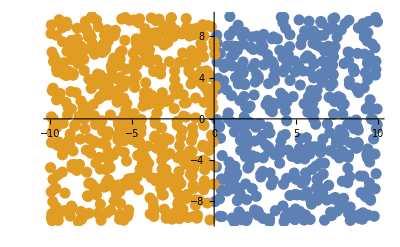

```mathematica
ListPlot[Evaluate[GatherBy[RandomReal[{-10,10},{1000,2}],Round[trainedclassifierNet[#]]&]],PlotStyle->{PointSize[.02]}]
```

我们的网络学会了我们想要学习的东西！

只需更改自由参数以最小化损失函数即可。

## 经典示例：手写数字识别

#### 探索 MNIST 数据库

MNIST 手写数字数据库是一个大型手动策选数据集的经典示例——收集和分类输入数据的艰巨任务已经为您完成！

```mathematica
digitsResource = ResourceObject["MNIST"]
```

ResourceObject[…]

```mathematica
digitsTrainingData=ResourceData[digitsResource,"TrainingData"];
```

```mathematica
RandomSample[digitsTrainingData,5]
```

{-Graphics-→7,-Graphics-→9,-Graphics-→6,-Graphics-→3,-Graphics-→7}

#### 预训练网络

神经网络最简单的例子通常是手写数字分类.  Wolfram 神经网络存储库中提供了一个经过 MNIST 数据预训练的合适网络：

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
lenetModel[-Graphics-]
```

6

```mathematica
lenetModel[-Graphics-]
```

7

我们还可以下载未经训练的网络版本，或使用 NetInitialize[...,All] 将网络中的所有权重重置为随机配置：

```mathematica
untrainedLeNet=NetInitialize[lenetModel,All]
```

NetChain[<>]

```mathematica
RandomSample[digitsTrainingData,5]
```

{-Graphics-→3,-Graphics-→1,-Graphics-→8,-Graphics-→8,-Graphics-→3}

```mathematica
untrainedLeNet[Keys[%]]
```

{2,2,2,2,2}

有关训练和使用此网络的更多详细信息，请参见神经网络简介教程.

## 使用 MNIST 数据库的变分自动编码器

```mathematica
Quit
```

#### 介绍

现在，我们旨在创建一个表示手写数字特征的编码器. 为此，我们从头开始构建，然后训练一个网络，该网络首先将图像“编码”为压缩的演示文稿，然后将其“解码”为图像. 比较输出图像和输入图像可以训练网络. 恢复已训练网络的第一部分将产生所需的编码器.

这个例子看出使用 Wolfram 语言演示神经网络框架的几个有用方面，并说明了我们先前关于神经网络从大量数据中提取基本信息的优势的观点.

#### 变分自动编码器

我们想要将 MNIST 图像（编码为 784 = 28×28 个实数）减少到八个实数，然后从这八个实数中重建原始图像：

```mathematica
encoderChain=NetChain[{ReshapeLayer[{1,28,28}],ConvolutionLayer[64,{14,14}],ElementwiseLayer[Max[Ramp[#],0.3#]&],DropoutLayer[],ConvolutionLayer[64,{8,8}],ElementwiseLayer[Max[Ramp[#],0.3#]&],DropoutLayer[],ConvolutionLayer[64,{2,2},"PaddingSize"->1],ElementwiseLayer[Max[Ramp[#],0.3#]&],DropoutLayer[],FlattenLayer[],LinearLayer[8]}]
```

NetChain[<>]

然后，我们希望从这八个参数中尽可能地重建原始图像：

```mathematica
decoderChain=NetChain[{LinearLayer[25],ElementwiseLayer[Max[Ramp[#],0.3#]&],LinearLayer[49],ElementwiseLayer[Max[Ramp[#],0.3#]&],ReshapeLayer[{1,7,7}],DeconvolutionLayer[64,{6,6}],ElementwiseLayer[Ramp],DropoutLayer[],DeconvolutionLayer[64,4,"PaddingSize"->2],ElementwiseLayer[Ramp],DropoutLayer[],DeconvolutionLayer[64,4,"PaddingSize"->2],ElementwiseLayer[Ramp],FlattenLayer[],LinearLayer[784],ElementwiseLayer[LogisticSigmoid],ReshapeLayer[{1,28,28}]},"Input"->8]
```

NetChain[<>]

还有一些有关 VAE 的其他技术细节，其中包括假设错误分布正常. 在本示例中，我们将忽略这些细节，但是它们将是该主题论文的突出特征. 有关更多详细信息，请参见D. P. Kingma 和 M. Welling 撰写的“An Introduction to Variational Autoencoders” .

#### 网络链拟合进网络图

我们指定要包含在总 NetGraph 中的链或子图. 我们为它们分配名称，并指定它们如何组合在一起：

```mathematica
totalgraph=NetInitialize@NetGraph[
<|
"encoder"->encoderChain,
"decoder"->decoderChain
|>,

{
NetPort["Input"]->"encoder"->"decoder"->NetPort["Output"]
},
"Input"->  NetEncoder[{"Image",{28,28},ColorSpace->"Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]]
```

NetGraph[<>]

注意：为了更好地说明，此处使用 NetGraph 代替了部分 NetChain，同时在几张幻灯片中也简化了我们的网络手术.

## 训练变分自动编码器

#### 训练

MNIST 数据库提供了我们用作输入和所需输出的手写数字图像. 在合理的时间内训练此网络需要使用 GPU：

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
```

```mathematica
trainedNet=NetTrain[totalgraph,<|"Input"->Keys[trainingData],"Output"->Keys[trainingData]|>,TargetDevice->"CPU"] (* change to GPU for faster training *)
```

$Aborted

或者，可以从Wolfram Cloud中下载经过预训练的网络：

```mathematica
trainedNet=CloudGet[CloudObject["https://www.wolframcloud.com/obj/fed66ddf-fa49-46a7-8df2-c7c9137e0922"]]
```

NetGraph[<>]

请注意，我们未指定 LossFunction. 默认行为是指定的输入应与指定的输出最大程度地匹配，以最小化差的平方.

完成所有操作后，网络可以将有关数字图像的信息减少到 8 个实数，然后以较高的精度重构原始数字：

```mathematica
test=Keys[RandomSample[trainingData,10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsGrid[Transpose[{test,trainedNet/@test}]]
```

-Graphics-

## 网络手术

#### 将神经网络分开

对于已经训练好的并具有一组指定网络层的神经网络，我们可以提取该网络的各个部分，并查看每个部分各自的作用：

```mathematica
encoderSubnet=NetTake[trainedNet,{"encoder","encoder"}]
```

NetGraph[<>]

通过仅使用“编码器”部分，我们可以看到手写数字图像如何映射到八个实数：

```mathematica
test[[2]]
```

-Graphics-

```mathematica
encoderSubnet[test[[2]]]
```

{-23.9281,-31.396,10.5851,-23.6572,65.718,9.51978,-84.1965,46.4559}

我们可以使用神经网络的“解码器”部分来查看网络如何从八个参数重建手写数字：

```mathematica
decoderSubnet=NetTake[trainedNet,{"decoder","decoder"}]
```

NetGraph[<>]

通过遍历参数空间的特定部分，我们可以在数字之间进行变形. 对于预训练的示例，这会将 7 变形为 2：

```mathematica
Manipulate[decoderSubnet[{x,30.,-35.5,16.3,-27.5,-23.2,-18.,35.1}],{{x,2.8},-40,50}]
```

我们还可以随机遍历参数空间，看看子网可以绘制出什么“数字”：

```mathematica
DynamicModule[{temp=RandomVariate[NormalDistribution[],8],outs},
Dynamic[
Refresh[
temp=temp+RandomVariate[NormalDistribution[],8];
outs=ImageResize[decoderSubnet[{temp}][[1]],500]
],
UpdateInterval->.01]
]
```

## 有趣的例子

#### Wolfram 神经网络存储库

神经网络存储库包含许多可以使用 NetModel 下载的经过预训练的网络.

#### 估计距相机的距离

网络模型计算深度图并将原始图像重新绘制为二进制图像：

```mathematica
depthmap=NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"];
mydepthmap=depthmap@ExampleData[{"TestImage","House2"}];
GraphicsRow[{ExampleData[{"TestImage","House2"}],ImageResize[ImageAdjust[Image[mydepthmap]],{512,512}]},ImageSize->1000]
```

-Graphics-

#### 从文本确定情感（注意：大下载量）：

```mathematica
sentimentScore[text_,device_:"CPU"]:=With[{output=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"LastState","Output"}],TargetDevice->device]},Switch[Depth[output],2,output[[2389]],3,output[[All,2389]]]]
```

```mathematica
sentimentScore["This course is lots of fun"]
```

0.00869283

```mathematica
sentimentScore["I dislike old cabin cruisers"]
```

-0.0193942

```mathematica
visualizeSentiment[text_String,device_:"CPU"]:=With[{sentiment=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"mLSTM","OutputState"}]][[All,2389]]},Grid[{MapThread[Item[Style[#1,Bold],Background->Opacity[0.75,#2]]&,{Characters[text],RGBColor[1-#,#,0]&/@Rescale[sentiment,{-0.1,0.1},{0,1}]}]},ItemSize->Small]]
```

```mathematica
visualizeSentiment["This course is lots of fun, the examples are instructive, but the lunch wasn't great"]
```

T | h | i | s |   | c | o | u | r | s | e |   | i | s |   | l | o | t | s |   | o | f |   | f | u | n | , |   | t | h | e |   | e | x | a | m | p | l | e | s |   | a | r | e |   | i | n | s | t | r | u | c | t | i | v | e | , |   | b | u | t |   | t | h | e |   | l | u | n | c | h |   | w | a | s | n | ' | t |   | g | r | e | a | t

# 网页操作

## 从网页上获取数据

#### Import

Import 可以多种形式从网站检索信息：

```mathematica
Import["https://www.wolfram.com/"]//(StringTake[#,400]&)
```

WolframAlpha.com   WolframCloud.com   All Sites & Public Resources...      
                    
  Products & Services  
 
 
 
 
Wolfram|One   Mathematica   Wolfram|Alpha Notebook Edition   Programming Lab   Finance Platform   SystemModeler   Wolfram Player   Wolfram Engine   WolframScript    
 
Enterprise Private Cloud   Enterprise Mathematica   Wolfram|Alpha Appliance     Enterprise Solutions

使用 Import 的第二个参数，我们可以指定要从网站检索的确切内容. 给第二个选项“Elements”将告诉我们哪些参数可用：

```mathematica
Import["https://www.wolfram.com/","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

我们可以从网页导入所有超链接：

```mathematica
Import["https://www.wolfram.com/","Hyperlinks"]//Short
```

{http://www.wolframalpha.com/?source=nav,«264»,http:/…t.com/}

我们还可以导入完整的 HTML 文档：

```mathematica
Import["https://www.wolfram.com/","Source"]//(StringTake[#,400]&)
```

<!doctype html>
<html lang="en" class="homepage">
<head>

<!-- begin framework head en -->

    <meta http-equiv="x-ua-compatible" content="ie=edge">
    <meta name="viewport" content="width=device-width, initial-scale=1">
    <meta charset="utf-8">
    <meta name="msapplication-config" content="/browserconfig.xml">
    <title>Wolfram: Computation Meets Knowledge</title>
    <meta name="descripti

导入图像：

```mathematica
Import["https://www.wolfram.com/","Images"]//Short
```

Import::htmlimg: Some images could not be imported.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

导入为“Data”将尝试将网站内容解释为数据表. 这对于从在线表格或电子表格中导入数据非常有用：

```mathematica
Import["https://www.wolfram.com/","Data"]//Shallow[#,5]&
```

{{{WolframAlpha.com ,WolframCloud.com ,All Sites & Public Resources... },{{«4»},{«4»},{«3»},{«3»}, }},{{{«4»}, Technical presentations with live computation ,{«2»}},{{«2»}, Technical presentations with live computation , Supercharged spreadsheets. Excel + the Wolfram Language ,{«2»}, A global resource for public data and data-backed publication—curated and structured for computation, visualization, analysis }},{{{«2»},{«4»},{«2»},{«13»},{«2»}},{Legal & Privacy Policy ,Site Map ,WolframAlpha.com ,WolframCloud.com }}}

#### 其他 URL 导入函数

URLDownload 可以将网页的全部内容存储在本地文件中：

```mathematica
URLDownload["https://wolfram.com"]
```

File[/private/var/folders/21/r9b6f46n6471sjfcst6jfrpm0000gn/T/index-42d4b9c3-eb6e-4950-a3c1-45208b0edb0a.html]

URLExecute 可以将参数发送到 URL，并指定其他选项（API 的理想选择）：

```mathematica
URLExecute["http://en.wikipedia.org/w/api.php",{"format"->"json","action"->"query","titles"->"Main Page"}]
```

{batchcomplete→,query→{pages→{15580374→{pageid→15580374,ns→0,title→Main Page}}}}

URLSubmit 表示可以执行 ScheduledTask 的 URLExecute 的任务版本.

URLRead 将请求发送到 URL 并读回响应，并将其作为“响应对象”返回，从中可以获取其他信息：

```mathematica
URLRead["http://wolfram.com"]
```

HTTPResponse[…]

还有一些较低级别的函数，例如 SocketConnect，还有更多的标头充当 HTTP 提交或响应的容器. 可以在此指南页面上找到完整列表.

## 部署到网页

#### 创建 HTML 内容

Export 函数可以将笔记本内容转换为 HTML，以便可以将其显示在网页上. 请注意，此内容将不是交互式的，并且所有方程式都将转换为静态图像.

在计算下一行之前，请打开 Wolfram 产品前端中包含的文件 testforHTML.nb：

```mathematica
SetDirectory[NotebookDirectory[]];
nb=NotebookOpen["~/Downloads/testforHTML.nb"];
```

```mathematica
Export["testForHTML.html",nb]
```

testForHTML.html

在互联网浏览器中快速打开 testForHTML.html，并验证测试笔记本的内容是否全部可见：

```mathematica
SystemOpen["testForHTML.html"]
```

#### 部署到云端

一旦注册了 Wolfram ID，就可以使用 Wolfram Cloud™.

CloudDeploy 将生成一个 CloudObject，然后您可以将其共享给 Wolfram Cloud 的其他用户：

```mathematica
CloudDeploy[
Manipulate[
Plot[Sin[a x],{x,0,2π},PlotRange->{-1,1}],
{{a,2},1,5}],
Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/70c44092-6cb6-42bd-b3f8-93dd75476bc2]

FormPage 将生成一个表单，可以在其中输入查询，并且可以使用 Wolfram 语言计算响应：

```mathematica
FormPage[{{"word","Enter a word:"}->"String"},"Your word was "<>ToString[StringLength[#word]] <>" letters long"&]
```

```mathematica
CloudDeploy[FormPage[{{"word","Enter a word:"}->"String"},"Your word was "<>ToString[StringLength[#word]] <>" letters long"&]]
```

CloudObject[https://www.wolframcloud.com/obj/2c78f4c1-645f-4256-8890-34f12ed76b9f]

API 函数也可以部署到云中：

```mathematica
func=APIFunction[{"x"->"Integer"},FactorInteger[#x]&];
```

```mathematica
func["x"->"15"]
```

{{3,1},{5,1}}

```mathematica
api=CloudDeploy[func]
```

CloudObject[https://www.wolframcloud.com/obj/3765d84b-5b67-4811-96a4-fd9573ee8a10]

```mathematica
URLExecute[api,{"format"->"json","action"->"query","x"->"15"}]
```

{{3, 1}, {5, 1}}

您还可以生成适当的代码，以将这些对象嵌入网站上的 iframe 中，或使用给定的语言与 API 联系：

```mathematica
EmbedCode[CloudDeploy["hello, world"]]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/obj/0ff0dfe0-a905-486e-9e9b-6ab14ce8243f?_embed=iframe" width="600" height="800"></iframe>

```mathematica
EmbedCode[APIFunction[{"i"->"Integer"},#i^2&],"Python"]
```

Embeddable Code
Use the files and code below to call the Wolfram Cloud function from Python:
Dependencies
  Install the [wolframclient](https://pypi.org/project/wolframclient) library.


Code
 | Copy to Clipboard
# -*- coding: utf-8 -*-

from __future__ import absolute_import, print_function, unicode_literals
from wolframclient.evaluation import WolframCloudSession

def call(i):
    """ Call the API using function input parameter values.
    If the API was deployed with an export formats set to JSON or WXF, the result is often a native Python type.
    """
    with WolframCloudSession() as session:
        api_response = session.call('https://www.wolframcloud.com/obj/9bc37185-0b2f-4715-8e37-bffd1d5e8b8b', {'i' : i})
        return api_response.get()

## 外部网络服务

#### 服务执行

Wolfram 语言可以连接到 Twitter、Dropbox 和 许多其他外部服务. 许多其他外部服务。

可以使用 ServiceExecute 直接进行查询：

```mathematica
ServiceExecute["Twitter","LastTweet",{"Username"->"stephen_wolfram"}]
```

Announcing a new pre-college / pre-grad-school educational initiative for 2021-22: Wolfram Gap Year Research Programs.  Accepting applications now!
https://t.co/3juPh2u100 https://t.co/6jyxbxPFiC

您还可以创建一个代表连接的 ServiceObject，然后可以将查询传递给：

```mathematica
arXiv=ServiceConnect["ArXiv"]
```

ServiceObject[…]

```mathematica
articles=arXiv["Search",{"Query"->"Solitons",MaxItems->4}];
```

```mathematica
articles[All,{"Title","Summary"}]
```

请注意，许多 ServiceExecute 连接要求您登录并验证该服务的帐户. 您可能还拥有数量有限的服务积分.

您可以通过评估来查看您拥有多少积分：

```mathematica
$ServiceCreditsAvailable
```

还有一些使用外部服务的函数，但未通过 ServiceExecute 显式调用.  WebSearch 和 WebImageSearch 函数使用 Bing 服务：

```mathematica
WebImageSearch["Dog","Country"->"China"]
```

WikipediaSearch 和 WikipediaData 函数可让您从维基百科文章中检索内容：

```mathematica
WikipediaData["Mathematica","TitleTranslationRules"]
```

{Arabic→ماثماتيكا,Azerbaijani→Mathematica,Bulgarian→Mathematica,Czech→Mathematica,Danish→Mathematica,German→Mathematica,Greek→Wolfram Mathematica,Spanish→Mathematica,Basque→Mathematica,Persian→مثمتیکا,Finnish→Mathematica,French→Mathematica,Hebrew→Mathematica,Hindi→मैथमेटिका,Hungarian→Mathematica,Indonesian→Mathematica,Italian→Mathematica,Japanese→Mathematica,Korean→매스매티카,Kyrgyz→Mathemateca,Lithuanian→Mathematica,Malayalam→മാത്തമാറ്റിക്ക,Dutch→Mathematica (software),Norwegian Bokmål→Mathematica,Polish→Mathematica,Portuguese→Mathematica,Russian→Mathematica,Scots→Wolfram Mathematica,Simple English→Wolfram Mathematica,Slovenian→Mathematica,Albanian→Mathematica,Serbian→Mathematica,Swedish→Mathematica,Turkish→Mathematica,Ukrainian→Mathematica,Vietnamese→Mathematica,Chinese→Wolfram Mathematica}

## 连接到实时浏览器会话

#### StartWebSession

使用函数 StartWebSession，您可以与浏览器进行交互，以编程方式点击并填写表单和字段.

首先，我们在选择的浏览器中启动实时网络会话：

```mathematica
session=StartWebSession["Chrome"]
```

WebSessionObject[…]

#### WebExecute

然后，我们使用 WebExecute 执行指定的操作. 在第一种情况下，我们使用“OpenPage”导航到我们喜欢的网站：

```mathematica
WebExecute[session,"OpenPage"->"https://www.wolframalpha.com"]
```

Success[…]

了解页面结构后，我们可以选择某些字段或表单：

```mathematica
input=WebExecute[session,"LocateElements"->"Tag"->"input"]//First
```

WebElementObject[…]

然后，我们可以将文本键入给定的元素，然后将其提交给指定的表单：

```mathematica
WebExecute[session,"TypeElement"->{input,"photon"}];
WebExecute[session,"SubmitElement"->input];
```

我们可以通过查询网页会话的当前 URL 来查看表单是否已在网页上处理：

```mathematica
WebExecute[session,"PageURL"]
```

https://www.wolframalpha.com/input/?i=photon

使用函数 DeleteObject 结束会话：

```mathematica
DeleteObject[session]
```

## 其他网络服务

#### 邮件服务

您还可以连接到现有的电子邮件服务并自动对其进行操作. 使用函数 SendMail 和 MailReceiverFunction，您可以自动发送和接收电子邮件.

可以执行此操作以自动发送报告. 作为一个简单的示例，您可以 CloudDeploy 一个每小时检查一次当前温度的任务：

```mathematica
obj=CloudDeploy[
ScheduledTask[
If[
Quantity[30., "DegreesCelsius"]>AirTemperatureData[GeoPosition[{40.67,-73.94}]] >Quantity[20., "DegreesCelsius"], 
SendMail["mymail@mymail.com","Finally, the weather is nice!"]
],
"Hourly"]
]
```

还有许多其他函数可用于导入某些文件夹/消息. 您还可以定义 MailReceiverFunction 或 MailResponseFunction 来指定如何处理某些消息.

#### 消息

SendMessage 可用于将消息发送到各种渠道：

```mathematica
CellPrint[ExpressionCell[Grid[{
{"Email","email"},
{"Facebook","Facebook status update"},
{"LinkedIn","LinkedIn status update"},
{"MMS","MMS message"},
{"SMS","SMS text message"},
{"Twitter","Twitter post"}
},
Alignment->Left,BaseStyle->{FontFamily->"Times",FontColor->GrayLevel[0.15],FontSize->14},
Frame->True,
Background->RGBColor[1,1,0.85],
Spacings->{4,2}],"Output",GeneratedCell->False]]
```

Email | email
Facebook | Facebook status update
LinkedIn | LinkedIn status update
MMS | MMS message
SMS | SMS text message
Twitter | Twitter post

发送短信：

```mathematica
$MobilePhone
```

```mathematica
SendMessage["SMS","This is a text message from the Wolfram Language"]
```

Success[…]

# 图像处理

## 基本图像处理

Wolfram 语言具有广泛的 基本图像处理功能：

```mathematica
testimg= ExampleData[{"TestImage","Mandrill"}]
```

```mathematica
ImageTrim[testimg,{{100,100},{300,300}}]
```

```mathematica
ImageResize[testimg,64]
```

```mathematica
ImageRotate[testimg,π/6]
```

```mathematica
ColorNegate[testimg]
```

```mathematica
Binarize[testimg]
```

## 分量运算

Wolfram 语言还具有探索和识别图像成分的函数.

MorphologicalComponents 函数尝试将图像划分为连续的元素，并为每个独立的分量分配一个指标.

为了消除噪音，我们可以使用函数 DeleteSmallComponents：

```mathematica
DeleteSmallComponents[-Graphics-]
```

-Graphics-

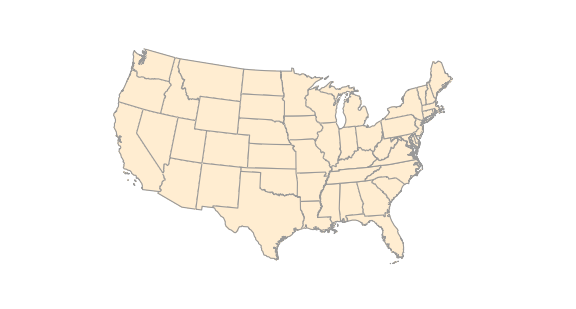

```mathematica
continentalUSMap=GeoGraphics[{GeoStyling["OutlineMap"],Polygon[LinguisticAssistant]},GeoBackground->None,ImageSize->Large]
```

我们选择适当的 Binarize 阈值，以使分界线清晰：

```mathematica
Binarize[continentalUSMap,.9]
```

-Graphics-

```mathematica
MorphologicalComponents[continentalUSMap,.9]//Colorize
```

-Graphics-

尽管函数在非常狭窄和/或不规则的形状中表现不好（请参见弗吉尼亚州，西弗吉尼亚州和马里兰州的交界），但它能够为我们很好地估计不同实体的数量. 通过使用 DeleteSmallComponents 函数删除给定像素数以下的分量，可以部分解决这些问题：

```mathematica
MorphologicalComponents[DeleteSmallComponents[Binarize[continentalUSMap,.9],10]]//Colorize
```

-Graphics-

```mathematica
Max[MorphologicalComponents[DeleteSmallComponents[Binarize[continentalUSMap,.9],10]]]
```

## 像素运算

图像存储为红 - 绿 - 蓝（RGB）值的数组：

```mathematica
(testdata=ImageData[testimg])//Short
```

{{«1»},«510»,{{0.0352941,«21»,«21»},«510»,{«1»}}}

```mathematica
testdata[[1]]
```

{{0.643137,0.588235,0.278431},{0.247059,0.223529,0.121569},{0.294118,0.168627,0.0392157},{0.372549,0.368627,0.180392},{0.615686,0.54902,0.286275},{0.388235,0.380392,0.129412},{0.356863,0.2,0.152941},{0.2,0.0980392,0.117647},{0.333333,0.27451,0.14902},{0.431373,0.258824,0.176471},{0.443137,0.356863,0.160784},{0.588235,0.615686,0.290196},{0.67451,0.607843,0.368627},{0.517647,0.435294,0.105882},{0.360784,0.290196,0.113725},{0.623529,0.596078,0.329412},{0.768627,0.764706,0.333333},{0.533333,0.498039,0.176471},{0.392157,0.301961,0.168627},{0.368627,0.4,0.156863},{0.317647,0.294118,0.164706},{0.4,0.360784,0.188235},{0.4,0.443137,0.192157},{0.262745,0.282353,0.133333},{0.278431,0.301961,0.176471},{0.454902,0.494118,0.427451},{0.498039,0.494118,0.301961},{0.364706,0.254902,0.164706},{0.239216,0.239216,0.0980392},{0.521569,0.658824,0.254902},{0.701961,0.701961,0.501961},{0.27451,0.254902,0.247059},{0.278431,0.282353,0.188235},{0.498039,0.580392,0.419608},{0.458824,0.603922,0.482353},{0.309804,0.376471,0.278431},{0.356863,0.294118,0.211765},{0.207843,0.27451,0.0980392},{0.698039,0.717647,0.329412},{0.482353,0.294118,0.262745},{0.25098,0.101961,0.0431373},{0.321569,0.294118,0.0509804},{0.662745,0.701961,0.152941},{0.662745,0.670588,0.219608},{0.219608,0.278431,0.101961},{0.419608,0.494118,0.137255},{0.266667,0.435294,0.25098},{0.533333,0.533333,0.156863},{0.584314,0.592157,0.352941},{0.392157,0.462745,0.239216},{0.356863,0.305882,0.113725},{0.517647,0.490196,0.113725},{0.470588,0.498039,0.168627},{0.47451,0.47451,0.152941},{0.686275,0.690196,0.243137},{0.760784,0.741176,0.454902},{0.607843,0.596078,0.419608},{0.443137,0.411765,0.105882},{0.67451,0.72549,0.266667},{0.596078,0.65098,0.447059},{0.34902,0.360784,0.196078},{0.666667,0.709804,0.227451},{0.803922,0.784314,0.501961},{0.443137,0.552941,0.247059},{0.745098,0.690196,0.317647},{0.556863,0.556863,0.25098},{0.596078,0.592157,0.227451},{0.6,0.635294,0.239216},{0.686275,0.764706,0.588235},{0.6,0.65098,0.490196},{0.396078,0.470588,0.192157},{0.690196,0.647059,0.223529},{0.403922,0.309804,0.176471},{0.309804,0.243137,0.160784},{0.415686,0.482353,0.258824},{0.466667,0.482353,0.298039},{0.52549,0.52549,0.27451},{0.443137,0.47451,0.223529},{0.290196,0.247059,0.141176},{0.494118,0.54902,0.129412},{0.776471,0.839216,0.384314},{0.560784,0.666667,0.486275},{0.294118,0.258824,0.188235},{0.266667,0.282353,0.203922},{0.211765,0.168627,0.168627},{0.160784,0.152941,0.121569},{0.337255,0.427451,0.0941176},{0.376471,0.345098,0.223529},{0.509804,0.454902,0.184314},{0.360784,0.415686,0.0745098},{0.721569,0.8,0.384314},{0.780392,0.827451,0.690196},{0.384314,0.466667,0.447059},{0.32549,0.286275,0.133333},{0.2,0.101961,0.121569},{0.235294,0.192157,0.184314},{0.184314,0.184314,0.105882},{0.439216,0.541176,0.243137},{0.392157,0.498039,0.435294},{0.403922,0.360784,0.333333},{0.329412,0.376471,0.2},{0.427451,0.52549,0.305882},{0.560784,0.537255,0.458824},{0.384314,0.427451,0.196078},{0.360784,0.486275,0.278431},{0.584314,0.623529,0.403922},{0.419608,0.4,0.180392},{0.572549,0.635294,0.439216},{0.647059,0.678431,0.470588},{0.533333,0.592157,0.313725},{0.584314,0.615686,0.47451},{0.443137,0.396078,0.243137},{0.376471,0.490196,0.317647},{0.568627,0.690196,0.54902},{0.490196,0.611765,0.6},{0.607843,0.666667,0.509804},{0.627451,0.564706,0.301961},{0.423529,0.54902,0.270588},{0.396078,0.486275,0.356863},{0.270588,0.266667,0.203922},{0.439216,0.494118,0.211765},{0.568627,0.67451,0.556863},{0.52549,0.647059,0.662745},{0.439216,0.552941,0.454902},{0.556863,0.713725,0.72549},{0.658824,0.694118,0.654902},{0.388235,0.533333,0.352941},{0.752941,0.815686,0.701961},{0.537255,0.607843,0.596078},{0.662745,0.721569,0.498039},{0.388235,0.623529,0.376471},{0.729412,0.796078,0.694118},{0.54902,0.607843,0.552941},{0.494118,0.588235,0.270588},{0.678431,0.752941,0.564706},{0.603922,0.721569,0.545098},{0.47451,0.541176,0.478431},{0.203922,0.207843,0.270588},{0.32549,0.286275,0.168627},{0.376471,0.458824,0.294118},{0.682353,0.745098,0.721569},{0.309804,0.380392,0.419608},{0.415686,0.639216,0.411765},{0.572549,0.756863,0.776471},{0.513725,0.701961,0.627451},{0.305882,0.478431,0.45098},{0.411765,0.52549,0.411765},{0.607843,0.705882,0.411765},{0.403922,0.647059,0.529412},{0.623529,0.67451,0.576471},{0.27451,0.235294,0.313725},{0.203922,0.25098,0.184314},{0.294118,0.380392,0.211765},{0.313725,0.498039,0.34902},{0.239216,0.427451,0.345098},{0.235294,0.207843,0.211765},{0.2,0.286275,0.176471},{0.290196,0.462745,0.454902},{0.278431,0.266667,0.364706},{0.176471,0.203922,0.184314},{0.345098,0.458824,0.286275},{0.329412,0.321569,0.294118},{0.278431,0.360784,0.192157},{0.505882,0.6,0.294118},{0.690196,0.67451,0.380392},{0.25098,0.32549,0.2},{0.54902,0.580392,0.286275},{0.317647,0.431373,0.231373},{0.188235,0.337255,0.203922},{0.156863,0.215686,0.2},{0.337255,0.333333,0.152941},{0.356863,0.439216,0.243137},{0.431373,0.580392,0.458824},{0.458824,0.54902,0.34902},{0.454902,0.529412,0.337255},{0.337255,0.486275,0.356863},{0.423529,0.47451,0.341176},{0.603922,0.654902,0.419608},{0.482353,0.588235,0.407843},{0.603922,0.654902,0.45098},{0.678431,0.74902,0.568627},{0.431373,0.654902,0.635294},{0.596078,0.701961,0.631373},{0.337255,0.376471,0.411765},{0.227451,0.305882,0.254902},{0.403922,0.392157,0.219608},{0.25098,0.301961,0.129412},{0.47451,0.658824,0.376471},{0.560784,0.670588,0.662745},{0.231373,0.231373,0.286275},{0.231373,0.290196,0.180392},{0.219608,0.286275,0.156863},{0.458824,0.596078,0.423529},{0.615686,0.721569,0.666667},{0.513725,0.607843,0.552941},{0.329412,0.219608,0.254902},{0.235294,0.352941,0.235294},{0.454902,0.619608,0.541176},{0.596078,0.694118,0.721569},{0.572549,0.701961,0.698039},{0.705882,0.784314,0.670588},{0.658824,0.72549,0.705882},{0.537255,0.658824,0.705882},{0.47451,0.541176,0.537255},{0.54902,0.631373,0.490196},{0.584314,0.666667,0.521569},{0.588235,0.694118,0.682353},{0.603922,0.662745,0.572549},{0.623529,0.678431,0.611765},{0.458824,0.564706,0.619608},{0.392157,0.360784,0.356863},{0.439216,0.501961,0.282353},{0.603922,0.717647,0.627451},{0.521569,0.623529,0.662745},{0.298039,0.32549,0.333333},{0.301961,0.384314,0.341176},{0.298039,0.243137,0.270588},{0.313725,0.278431,0.176471},{0.333333,0.439216,0.329412},{0.498039,0.611765,0.666667},{0.54902,0.67451,0.682353},{0.568627,0.741176,0.694118},{0.631373,0.74902,0.764706},{0.694118,0.752941,0.776471},{0.494118,0.560784,0.454902},{0.454902,0.611765,0.509804},{0.588235,0.709804,0.741176},{0.294118,0.458824,0.498039},{0.227451,0.352941,0.188235},{0.380392,0.403922,0.384314},{0.211765,0.243137,0.235294},{0.2,0.227451,0.101961},{0.580392,0.694118,0.478431},{0.47451,0.662745,0.686275},{0.47451,0.568627,0.603922},{0.490196,0.643137,0.65098},{0.447059,0.596078,0.666667},{0.537255,0.662745,0.666667},{0.623529,0.752941,0.733333},{0.537255,0.67451,0.784314},{0.184314,0.376471,0.384314},{0.384314,0.494118,0.396078},{0.368627,0.501961,0.392157},{0.568627,0.67451,0.670588},{0.215686,0.294118,0.352941},{0.341176,0.501961,0.360784},{0.521569,0.619608,0.690196},{0.286275,0.309804,0.380392},{0.227451,0.298039,0.337255},{0.54902,0.694118,0.635294},{0.498039,0.662745,0.631373},{0.564706,0.737255,0.572549},{0.517647,0.603922,0.682353},{0.286275,0.270588,0.301961},{0.309804,0.356863,0.188235},{0.337255,0.501961,0.396078},{0.537255,0.643137,0.635294},{0.207843,0.215686,0.309804},{0.184314,0.262745,0.164706},{0.352941,0.454902,0.376471},{0.27451,0.356863,0.45098},{0.254902,0.321569,0.188235},{0.447059,0.588235,0.486275},{0.372549,0.533333,0.623529},{0.45098,0.580392,0.607843},{0.301961,0.301961,0.329412},{0.345098,0.458824,0.352941},{0.478431,0.654902,0.592157},{0.584314,0.756863,0.796078},{0.403922,0.576471,0.74902},{0.231373,0.294118,0.372549},{0.309804,0.34902,0.345098},{0.313725,0.368627,0.364706},{0.423529,0.619608,0.596078},{0.619608,0.729412,0.756863},{0.447059,0.65098,0.623529},{0.627451,0.776471,0.741176},{0.505882,0.678431,0.752941},{0.317647,0.403922,0.364706},{0.333333,0.462745,0.290196},{0.368627,0.403922,0.392157},{0.345098,0.443137,0.458824},{0.270588,0.298039,0.34902},{0.254902,0.305882,0.313725},{0.482353,0.627451,0.580392},{0.611765,0.8,0.847059},{0.717647,0.827451,0.854902},{0.580392,0.737255,0.772549},{0.588235,0.745098,0.788235},{0.513725,0.596078,0.631373},{0.47451,0.647059,0.592157},{0.505882,0.682353,0.768627},{0.486275,0.631373,0.627451},{0.407843,0.521569,0.462745},{0.501961,0.67451,0.678431},{0.396078,0.494118,0.537255},{0.466667,0.580392,0.545098},{0.596078,0.752941,0.729412},{0.654902,0.67451,0.733333},{0.286275,0.215686,0.329412},{0.164706,0.180392,0.188235},{0.352941,0.317647,0.396078},{0.415686,0.592157,0.611765},{0.462745,0.643137,0.647059},{0.439216,0.541176,0.615686},{0.219608,0.305882,0.392157},{0.227451,0.270588,0.270588},{0.627451,0.729412,0.643137},{0.576471,0.623529,0.745098},{0.286275,0.313725,0.427451},{0.380392,0.380392,0.380392},{0.584314,0.745098,0.627451},{0.713725,0.815686,0.815686},{0.678431,0.745098,0.823529},{0.482353,0.603922,0.537255},{0.45098,0.592157,0.423529},{0.588235,0.74902,0.823529},{0.592157,0.682353,0.682353},{0.443137,0.521569,0.360784},{0.741176,0.827451,0.784314},{0.611765,0.662745,0.701961},{0.294118,0.447059,0.4},{0.317647,0.403922,0.47451},{0.376471,0.517647,0.462745},{0.647059,0.764706,0.654902},{0.635294,0.788235,0.847059},{0.462745,0.65098,0.603922},{0.356863,0.596078,0.596078},{0.533333,0.709804,0.74902},{0.435294,0.505882,0.521569},{0.403922,0.541176,0.513725},{0.282353,0.388235,0.341176},{0.552941,0.662745,0.541176},{0.360784,0.588235,0.580392},{0.447059,0.619608,0.615686},{0.309804,0.411765,0.415686},{0.317647,0.388235,0.32549},{0.431373,0.623529,0.568627},{0.415686,0.556863,0.423529},{0.372549,0.568627,0.47451},{0.196078,0.4,0.411765},{0.305882,0.266667,0.254902},{0.313725,0.462745,0.45098},{0.258824,0.368627,0.301961},{0.454902,0.505882,0.301961},{0.654902,0.772549,0.678431},{0.47451,0.537255,0.619608},{0.27451,0.282353,0.278431},{0.364706,0.513725,0.427451},{0.6,0.690196,0.592157},{0.47451,0.552941,0.490196},{0.545098,0.686275,0.764706},{0.290196,0.396078,0.403922},{0.576471,0.639216,0.431373},{0.533333,0.682353,0.639216},{0.32549,0.478431,0.458824},{0.333333,0.301961,0.301961},{0.219608,0.223529,0.235294},{0.301961,0.278431,0.184314},{0.305882,0.431373,0.262745},{0.486275,0.658824,0.682353},{0.443137,0.482353,0.556863},{0.215686,0.270588,0.176471},{0.45098,0.564706,0.447059},{0.6,0.717647,0.694118},{0.501961,0.501961,0.411765},{0.427451,0.541176,0.529412},{0.611765,0.701961,0.619608},{0.494118,0.466667,0.482353},{0.278431,0.396078,0.427451},{0.407843,0.470588,0.52549},{0.45098,0.596078,0.576471},{0.552941,0.639216,0.635294},{0.560784,0.709804,0.760784},{0.490196,0.611765,0.541176},{0.356863,0.45098,0.498039},{0.392157,0.517647,0.603922},{0.215686,0.247059,0.254902},{0.356863,0.490196,0.4},{0.537255,0.701961,0.752941},{0.380392,0.482353,0.556863},{0.215686,0.2,0.247059},{0.305882,0.266667,0.278431},{0.396078,0.368627,0.360784},{0.423529,0.462745,0.360784},{0.454902,0.52549,0.521569},{0.705882,0.811765,0.776471},{0.74902,0.776471,0.847059},{0.360784,0.427451,0.505882},{0.498039,0.568627,0.447059},{0.529412,0.658824,0.568627},{0.65098,0.768627,0.803922},{0.6,0.686275,0.701961},{0.545098,0.678431,0.584314},{0.682353,0.792157,0.815686},{0.619608,0.666667,0.717647},{0.34902,0.462745,0.4},{0.509804,0.65098,0.65098},{0.6,0.666667,0.662745},{0.576471,0.760784,0.737255},{0.662745,0.756863,0.815686},{0.47451,0.45098,0.454902},{0.270588,0.352941,0.192157},{0.411765,0.560784,0.423529},{0.537255,0.615686,0.643137},{0.329412,0.403922,0.298039},{0.427451,0.501961,0.305882},{0.682353,0.792157,0.721569},{0.619608,0.741176,0.756863},{0.592157,0.662745,0.513725},{0.466667,0.572549,0.470588},{0.619608,0.6,0.501961},{0.435294,0.427451,0.321569},{0.631373,0.682353,0.458824},{0.556863,0.639216,0.564706},{0.392157,0.439216,0.356863},{0.313725,0.309804,0.317647},{0.423529,0.505882,0.352941},{0.427451,0.596078,0.537255},{0.556863,0.666667,0.698039},{0.388235,0.372549,0.364706},{0.309804,0.243137,0.137255},{0.447059,0.580392,0.407843},{0.6,0.709804,0.666667},{0.470588,0.545098,0.494118},{0.470588,0.403922,0.411765},{0.243137,0.223529,0.223529},{0.329412,0.317647,0.192157},{0.392157,0.411765,0.313725},{0.415686,0.411765,0.254902},{0.290196,0.27451,0.25098},{0.439216,0.462745,0.25098},{0.733333,0.796078,0.592157},{0.639216,0.764706,0.65098},{0.541176,0.65098,0.505882},{0.764706,0.74902,0.572549},{0.447059,0.517647,0.376471},{0.74902,0.784314,0.403922},{0.835294,0.854902,0.721569},{0.752941,0.694118,0.678431},{0.415686,0.407843,0.294118},{0.631373,0.705882,0.509804},{0.647059,0.713725,0.690196},{0.584314,0.658824,0.635294},{0.607843,0.545098,0.45098},{0.533333,0.552941,0.4},{0.690196,0.690196,0.52549},{0.788235,0.843137,0.67451},{0.796078,0.866667,0.733333},{0.654902,0.733333,0.647059},{0.6,0.658824,0.45098},{0.478431,0.6,0.462745},{0.584314,0.678431,0.482353},{0.529412,0.521569,0.403922},{0.32549,0.235294,0.341176},{0.4,0.396078,0.286275},{0.454902,0.337255,0.239216},{0.584314,0.556863,0.27451},{0.831373,0.866667,0.658824},{0.788235,0.8,0.596078},{0.741176,0.74902,0.509804},{0.796078,0.811765,0.560784},{0.698039,0.643137,0.470588},{0.521569,0.447059,0.345098},{0.396078,0.407843,0.235294},{0.4,0.556863,0.211765},{0.513725,0.494118,0.286275},{0.439216,0.498039,0.243137},{0.607843,0.662745,0.278431},{0.780392,0.8,0.517647},{0.764706,0.745098,0.572549},{0.572549,0.478431,0.317647},{0.517647,0.592157,0.301961},{0.678431,0.72549,0.45098},{0.686275,0.698039,0.541176},{0.764706,0.760784,0.498039},{0.47451,0.54902,0.352941},{0.560784,0.572549,0.352941},{0.729412,0.658824,0.231373},{0.572549,0.568627,0.294118},{0.745098,0.784314,0.698039},{0.623529,0.584314,0.466667},{0.301961,0.407843,0.223529},{0.537255,0.666667,0.47451},{0.666667,0.72549,0.705882},{0.643137,0.607843,0.572549},{0.54902,0.615686,0.407843},{0.741176,0.768627,0.521569},{0.533333,0.6,0.345098},{0.784314,0.792157,0.443137},{0.694118,0.709804,0.478431},{0.662745,0.682353,0.364706},{0.721569,0.772549,0.368627},{0.74902,0.807843,0.486275},{0.776471,0.741176,0.431373},{0.329412,0.301961,0.172549},{0.552941,0.603922,0.188235},{0.709804,0.701961,0.584314},{0.341176,0.380392,0.356863},{0.25098,0.278431,0.133333},{0.427451,0.372549,0.282353},{0.305882,0.294118,0.270588},{0.262745,0.235294,0.137255},{0.337255,0.462745,0.188235},{0.639216,0.690196,0.388235},{0.52549,0.513725,0.266667},{0.368627,0.301961,0.137255},{0.27451,0.278431,0.215686},{0.568627,0.545098,0.254902},{0.458824,0.466667,0.266667},{0.552941,0.666667,0.396078},{0.701961,0.737255,0.462745}}

我们可以将函数直接应用于图像中的 RGB 值以获得一些有趣的效果

```mathematica
Round[{0.5529411764705883,0.6666666666666666,0.396078431372549}]
```

{1,1,0}

```mathematica
ImageApply[Round,testimg]
```

我们也可以制作一些更多创意的函数. 这将 RGB 值的最大值设置为 1，其他设置为 0：

```mathematica
f@{0.5529411764705883,0.6666666666666666,0.396078431372549}
```

{0,1,0}

```mathematica
f[{r_,g_,b_}]:=Sign[{r,g,b}-Max[{r,g,b}]]+1
ImageApply[f,testimg]
```

我们可以发挥创造力，创建更复杂的函数. 这个模拟了狭义相对论的影响：

```mathematica
redshiftImage[x_List,f_?NumberQ]:=Module[{c1,c2,c3},
(c1= List@@ColorData["VisibleSpectrum"][Sqrt[(1-f)/(1+f)]630];c2= List@@ColorData["VisibleSpectrum"][Sqrt[(1-f)/(1+f)]540];c3= List@@ColorData["VisibleSpectrum"][Sqrt[(1-f)/(1+f)]465];Image[Map[#[[1]]c1+#[[2]]c2+#[[3]]c3&,x,{2}]])]
```

如果某个物体以相当大的速度向着您或远离您移动，则它会出现蓝移或红移，直到超出可见光谱并进入红外或紫外线为止：

```mathematica
Manipulate[redshiftImage[testdata,f],{{f,-.17,"Velocity / C"},-.5,.5,.01}]
```

将图像转换为灰度，同时保留红色：

```mathematica
ImageApply[If[#⟦1⟧>#⟦2⟧+#⟦3⟧,#,ConstantArray[Mean[#],3]]&,-Graphics-]
```

为灰度图像着色：

```mathematica
ImageApply[ {Sin[Pi #*4], Sin[Pi #], Sin[Pi # * 3]}&, -Graphics-]
```

## 卷积

由于图像存储为数组，因此我们还可以对它们执行其他矩阵运算.

由于图像只是一个大数组，因此从像素方式进行操作的下一个自然步骤是考虑依赖于给定像素及其邻域的操作：

```mathematica
GraphicsRow[{testimg,ImageConvolve[testimg,GaussianMatrix[10]]},ImageSize->700]
```

我们可以考虑对给定像素及其相邻像素求加权平均值以实现模糊. 通过使用 ListConvolve 函数，我们可以达到完全相同的效果（尽管在指定要将卷积应用于哪个级别的表达式时要格外小心）：

```mathematica
ListConvolve[{x,y},{1,2,3,4,5,6}]
```

{2 x+y,3 x+2 y,4 x+3 y,5 x+4 y,6 x+5 y}

```mathematica
Image[Transpose[ListConvolve[GaussianMatrix[10],#]&/@Transpose[testdata,{3,2,1}],{3,2,1}]]
```

通过使用矩阵的结构，可以实现特定方向的模糊.

对角模糊：

```mathematica
IdentityMatrix[27]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
ImageConvolve[testimg,IdentityMatrix[27]/27]
```

水平模糊：

```mathematica
ImageConvolve[-Graphics-,ConstantArray[1/20,{1,20}]]
```

-Graphics-

垂直模糊：

```mathematica
ImageConvolve[-Graphics-,Transpose[{Table[1/25,25]}]]
```

-Graphics-

图像卷积有一些实际用途，例如检测边缘（此处使用 Sobel operator）：

```mathematica
testimg2=ExampleData[{"TestImage","House"}]
```

```mathematica
edgedetectedimage=ImageApply[1/2 Norm[#]^2&,ImageConvolve[testimg2,({{-1, 0, 1}, {-2, 0, 2}, {-1, 0, 1}})]+ImageApply[1/2 Norm[#]^2&,ImageConvolve[testimg2,Transpose@({{-1, 0, 1}, {-2, 0, 2}, {-1, 0, 1}})]]]
```

还有一个用于边缘检测的内置函数：

```mathematica
EdgeDetect[testimg2]
```

## 图像还原

有许多函数使用卷积，逐像素运算或其他方法来还原图像.  这里有完整的列表.

对图像进行降噪：

```mathematica
MinFilter[-Graphics-,1]
```

-Graphics-

对图像进行去模糊处理：

```mathematica
ImageDeconvolve[-Graphics-,GaussianMatrix[10]]
```

-Graphics-

除了更基本的方法外， Inpaint  函数还可以对图像的受损或缺失部分进行极其精细的重建.

基本示例包括消除裂缝或变形：

```mathematica
Inpaint[-Graphics-, -Graphics-]
```

-Graphics-

## 神经网络与图像处理

#### 神经网络存储库

神经网络存储库包含许多用于处理图像的预训练神经网络.

#### 图像着色

```mathematica
NetModel["ColorNet Image Colorization Trained on ImageNet Competition Data"]
```

NetGraph[<>]

```mathematica
colorizeImage[img_Image]:=Image[Prepend[ArrayResample[NetModel["ColorNet Image Colorization Trained on ImageNet Competition Data"][img],Prepend[Reverse@ImageDimensions@img,2]],ImageData[ColorSeparate[img,"L"]]],Interleaving->False,ColorSpace->"LAB"]
```

原始灰度图像：

```mathematica
ExampleData[{"TestImage","Boat"}]
```

彩色化图像：

```mathematica
colorizeImage[ExampleData[{"TestImage","Boat"}]]
```

#### 将照片转换为梵高画作

```mathematica
vanGoghNet=NetModel["CycleGAN Photo-to-Van Gogh Translation"]
```

NetChain[<>]

原始图片：

```mathematica
ExampleData[{"TestImage","Peppers"}]
```

转换后的图片：

```mathematica
vanGoghNet[ExampleData[{"TestImage","Peppers"}]]
```

## 总结

计算神经网络模仿生物学习的方式

可以使用 NetChain 或 NetGraph 组合各种“层”以构建神经网络

NetTrain 可用于从训练数据集中训练网络

神经网络存储库中提供了各种各样的预训练网络

Wolfram 语言具有用于从 Web 导入数据的各种函数，包括 Import、URLDownload、URLRead 等.

用于将内容部署到 Web 的函数包括 Export、CloudDeploy、EmbedCode 等.

可以将各种外部服务连接到 Wolfram 语言并从中使用，包括 Twitter、arXiv 和 Bing 搜索.

讨论了 Wolfram 语言中的各种基本图像处理工具，例如 ImageTrim、ImageResize、ImageRotate 等.

逐像素和卷积运算可以应用于图像.

Wolfram 语言提供了多种还原图像的功能.